# Test of genetic algorithms - PIKAIA

```mathematica
dir=SetDirectory[NotebookDirectory[]];
```

## Goal

This notebook is used to prepare and discuss the PIKAIA tests. The examples are discussed in the Users Guide 1.0

## Module

This module (found in the net) is used for the output of numbers in FORTRAN format.

```mathematica
f77Eform[x_?NumericQ,fw_Integer,ndig_Integer]:=Module[{sig,s,p,ps},{s,p}=MantissaExponent[x];
{sig,ps}={ToString[Round[10^ndig Abs[s]]],ToString[Abs[p]]};
StringJoin@@Join[Table[" ",{fw-ndig-7}],If[x<0,"-"," "],{"0."},{sig},Table["0",{ndig-StringLength[sig]}],{"E"},If[p<0,{"-"},{"+"}],Table["0",{2-StringLength[ps]}],{ps}]]
```

## Maximizing a function of two variables

This example is discussed in section 5.1 page 35ff. The corresponding function is

```mathematica
f[x_,y_]:=Module[{r2,σ2,fu},r2=(x-0.5)^2+(y-0.5)^2;σ2=.15;n=9;fu=Cos[n π Sqrt[r2]]^2Exp[-r2/σ2];Return[fu]]
```

```mathematica
Plot3D[f[x,y],{x,0.,1.},{y,0.,1.},PlotPoints->50]
```

-Graphics3D-

The maximum is at (.5,.5) with f(.5,.5) = 1.0.

## Data for linear (chapter 5.2) and non-linear (chapter 5.3) least squares fit

The original distribution contained  test data. This data  set couldn’t be used. Thus the data are created according equation (5.11) on page 47.

#### Set the parameters

```mathematica
Clear[a,b,am,pm,fm]
```

```mathematica
a=1;b=20;
```

```mathematica
am={12.,10.,8.};
```

```mathematica
pm={20.,9.,7.5};
```

```mathematica
fm={.5,.8,.8};
```

```mathematica
del=0.5;n=200;
```

```mathematica
t={};f={};
```

#### Define the function

```mathematica
Do[tx=(i-1)*del;
    t=Append[t,tx];
   su=0.;
Do[su=su+am[[k]]*Sin[2.*π*(tx/pm[[k]]+fm[[k]])]
,{k,1,3}];
fx=a *tx +b+su;
f=Append[f,fx]
,{i,1,n}]
```

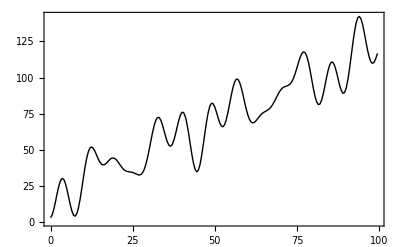

```mathematica
p1=ListPlot[Transpose[{t,f}],Joined->True,Frame->True,PlotStyle->{Black,Thick}]
```

#### Add noise

According to Fig. 5.4 on page 43 normally distributed noise with σ=5 is used to create a synthetic data set. The data that are used  in the present tests are defined in rn0. Other test data might be created.

```mathematica
data=RandomVariate[NormalDistribution[1,5],10^4];
```

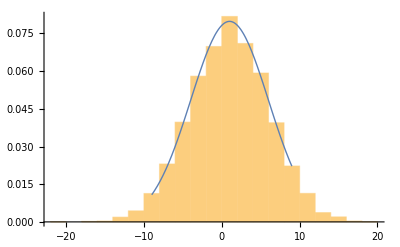

```mathematica
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,5],x],{x,-9,9},PlotStyle->Thick]]
```

```mathematica
rnu=RandomVariate[NormalDistribution[0.0,5],200]
```

```mathematica
rnu0={-4.598494158892377,-1.1233453774079716,-1.2145105640586107,-9.976128318405664,3.4103997542050553,-2.7749515762126524,-3.788372304776647,-3.530089970908604,1.7032805019701336,0.5862284188789515,0.5268636992483777,-0.6624241605443081,8.964339006013804,5.444502086417446,1.7550830563137496,-6.741762434875974,3.499010742536234,-2.2141543840830202,-4.175280439701212,9.80306893671703,-14.394251026002538,4.0958407521537,0.8546848183836251,1.3999377704629967,-1.1475837335551122,1.654791121994552,0.8401118780272196,-12.839267072845294,-5.392461647690904,2.5501671002320845,5.616693718209986,3.0981101379069735,-6.539552148658016,5.865219400842158,-6.881320770160931,-3.194590028173052,-2.7787813183470447,4.7658178792441275,-2.246442471826079,5.637551763110458,-1.0893139194535588,-0.9773044425847375,-1.0224682879430753,2.111230676960415,5.6422928157070125,2.7273055228841763,-2.140831644566557,-2.2319664432858604,-0.8484878020453996,-6.218169640007674,-2.9523652534972773,1.8358542992516687,0.10732753421798223,-6.039172550239857,-3.3037376092210646,-3.0760861105570334,2.2878348618986757,-0.9614779484608782,5.588256309932879,-6.93023810354627,-4.51683723082808,1.3028700404042548,3.9327061272853756,5.187262772654229,0.3575334201160535,-1.1770171770182478,-9.662990295792895,-1.7897650015655193,0.39542879160843325,-1.8081503664997587,9.188103759426616,0.6781173960619481,4.872252278574496,6.01211858543977,6.1576725353369826,-1.1616902151711852,0.9521770553091391,10.276043683910146,-3.9185348466878245,2.5530247221971,-6.218417615970249,4.766792857538202,-5.718937560239847,7.709562652905722,5.262468474720906,0.7864926747228758,5.876104099872159,1.9735283729291826,-0.6811341382157876,-1.0130069539300977,-5.189264637666747,13.577614265487284,-1.7680487685375992,-5.115802994564057,-1.672485524035277,-3.1677903333460424,-11.127702470066968,4.309646332338158,-0.7850659222753963,8.432995645258051,1.6668690290150354,-6.3459288345586256,4.144530049569464,-0.37434774584026964,3.313001700021463,9.030758230792975,0.32758967363765723,-11.262863427066888,7.948083401040574,8.534964098980659,-1.937598379494517,-0.6325460300214677,4.708993461112351,-5.193582744015018,-10.40139674700396,6.0009282058735165,1.3202533927382152,-10.87234770899986,-2.7075338241204903,-2.8594737110054185,-0.9317674972517801,-0.7307726010947242,-4.1043568343367784,1.9930323159510956,-6.1093296306138365,1.3927462592033706,2.5147167460368984,3.612450873680468,-2.342315903688723,-1.124007620332068,-1.0715733983209879,0.5513359841950953,-3.042077492967494,-4.459186088606862,0.12469634761998996,-3.679442152896981,2.6891245764629343,-5.41018964418012,0.9630118015495924,-7.501454783495693,1.062298786332155,-7.70107381143185,-0.08875289790982525,2.27615175168629,-5.166814848346262,-3.39684436040738,-5.103864025273935,-2.0585268716890344,-2.6488427099104928,-5.491576376206554,-0.24137739626319646,5.197939374167265,7.560110946717299,-3.248784698450168,0.6683991934478419,-3.390204264704109,1.635223625169512,4.624661255668017,-4.2976567865263675,-2.025267796766363,-8.228314123375444,-5.68502424548949,4.962874144524686,2.503719159680347,0.056318892369805855,-1.9659248490702064,3.505355127611714,-6.479285272617856,0.07454953572821502,-5.831044935344122,4.161560706730306,2.3516624687587067,-2.0957472967337814,1.8132229344401511,-1.24564116247453,-3.1146372678294405,0.1282502895026094,3.2927925998961074,8.988334845297514,1.016262969368188,-2.0518750434905657,0.38558159423805954,-2.9003025239778695,-1.6945461736226408,-12.069783394701421,-1.8019449126754215,-1.329220472756556,0.2961601276162577,0.9660582299331973,0.18294093179940848,9.033831250370948,-7.471401193362509,1.3462210149661666,3.454589856843518,7.560306653554571,2.1481783237946845,2.5150595697375473,6.4446264826560276,1.332459821065479,4.018160087835728};
```

```mathematica
f1=f+rnu0;
```

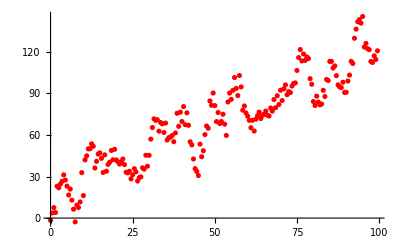

```mathematica
p2=ListPlot[Transpose[{t,f1}],PlotStyle->Red]
```

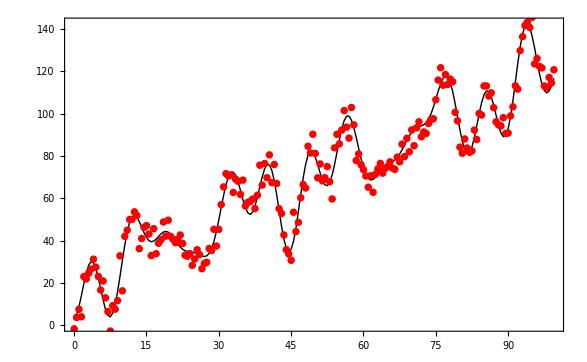

```mathematica
Show[p1,p2]
```

```mathematica
SetDirectory[dir<>"/../test/fit1b"];
```

Export data without noise

```mathematica
s=OpenWrite["test1.dat",FormatType->StandardForm];
Write[s,n]
Do[Write[s,f77Eform[t[[i]],14,6],"  ",f77Eform[f[[i]],14,6]]
,{i,1,n}]
Close[s];
```

Export data with noise

```mathematica
s1=OpenWrite["test1n.dat",FormatType->StandardForm];
Write[s1,n]
Do[Write[s1,f77Eform[t[[i]],14,6],"  ",f77Eform[f1[[i]],14,6]]
,{i,1,n}]
Close[s1];
```

## Chapter 5.2 - linear model

### Result from genetic algorithm

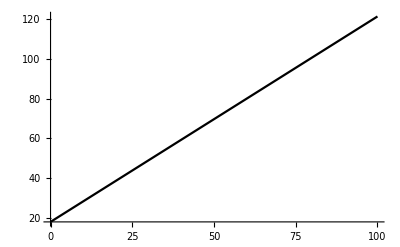

```mathematica
b=1.0365;a=17.786;p4=Plot[b x+a,{x,0,100},PlotStyle->{Black}]
```

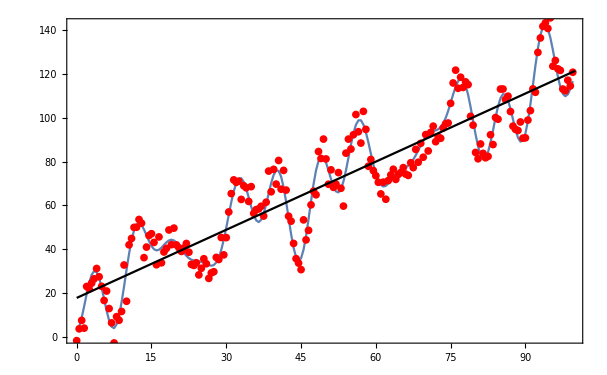

```mathematica
Show[p1,p2,p4]
```

### Linear regression with Mathematica

```mathematica
data=Transpose[{t,f1}];LinearModelFit[data,x,x]
```

FittedModel[17.7591+1.037 x]

The results from the genetic algorithm and the direct evaluation in Mathematica are very close.

## Chapter 5.3 - nonlinear model

```mathematica
SetDirectory[dir<>"/../test/fit1b"];
```

### Data from tutorial

The parameters found with the genetic algorithm, given in section 5.3 are given here. The sets will be used to compare with own calculations.

```mathematica
parm1={0.9999,19.21,10.30,9.044,0.8346};
```

```mathematica
parm3={0.9961,19.30,9.998,20.03,0.5124,7.346,8.927,0.7008,6.770,7.373,0.7011};
```

```mathematica
parm5={0.998,19.37,9.997,20.01,0.4999,9.828,9.020,0.8115,6.945,7.472,0.8001,20.01,44.60,0.6462,19.76,45.10,0.1643};
```

#### Define the function

```mathematica
ModelCurve[pp_,nf_]:=Module[{a,b,am,pm,fmdel,n,fa,t,tx,su,fx},
a=pp[[1]];b=pp[[2]];am={};pm={};fm={};
Do[
am=Append[am,pp[[3+(i-1)*3]]];
pm=Append[pm,pp[[4+(i-1)*3]]];
fm=Append[fm,pp[[5+(i-1)*3]]];
,{i,1,nf}];
del=0.5;n=200;t={};fa={};
Do[tx=(i-1)*del;
    t=Append[t,tx];
   su=0.;
Do[su=su+am[[k]]*Sin[2.*π*(tx/pm[[k]]+fm[[k]])]
,{k,1,nf}];
fx=a *tx +b+su;
fa=Append[fa,fx]
,{i,1,n}];
Return[Transpose[{t,fa}]]
]
```

### One Fourier mode

#### Data from file

```mathematica
nf=1;m=3*nf+2;Close["test1b1.res"];
```

```mathematica
parms={};Do[parms=Append[parms,Read["test1b1.res",{Number,Number}]],{m}];pp=Transpose[parms][[2]];
```

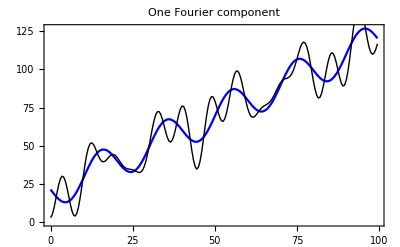

```mathematica
fm1=ModelCurve[pp,1];p1ca=ListPlot[fm1,Joined->True,Frame->True,PlotStyle->Blue,PlotLabel->"One Fourier component"];Show[p1ca,p1]
```

#### Data from tutorial

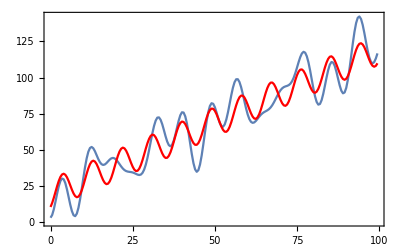

```mathematica
fm1=ModelCurve[parm1,1];p1tu=ListPlot[fm1,Joined->True,Frame->True,PlotStyle->Red];Show[p1,p1tu]
```

#### Comparison

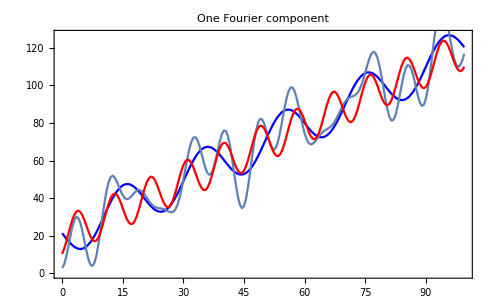

```mathematica
Show[p1ca,p1,p1tu]
```

### Three Fourier modes

#### Data from file

```mathematica
nf=3;m=3*nf+2;Close["test1b3.res"];
```

```mathematica
parms={};Do[parms=Append[parms,Read["test1b3.res",{Number,Number}]],{m}];pp=Transpose[parms][[2]];
```

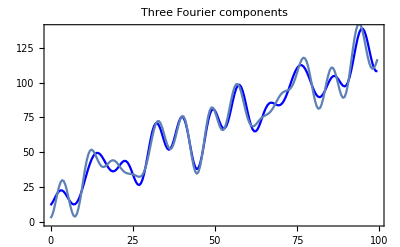

```mathematica
fm1=ModelCurve[pp,nf];p1ca=ListPlot[fm1,Joined->True,Frame->True,PlotStyle->Blue,PlotLabel->"Three Fourier components"];Show[p1ca,p1]
```

#### Data from tutorial

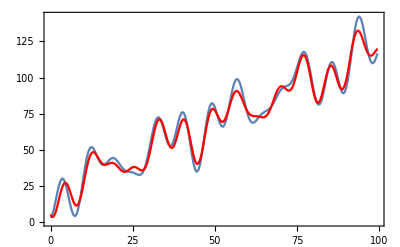

```mathematica
fm1=ModelCurve[parm3,3];p1tu=ListPlot[fm1,Joined->True,Frame->True,PlotStyle->Red];Show[p1,p1tu]
```

#### Comparison

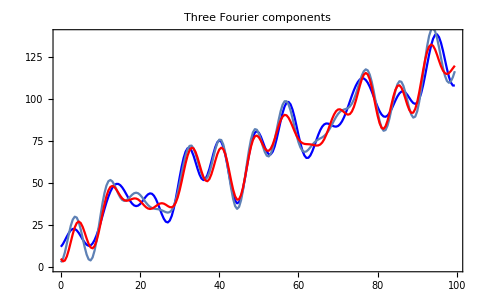

```mathematica
Show[p1ca,p1,p1tu]
```

### Five Fourier modes

#### Data from file

```mathematica
nf=5;m=3*nf+2;Close["test1b5.res"];
```

```mathematica
parms={};Do[parms=Append[parms,Read["test1b5.res",{Number,Number}]],{m}];pp=Transpose[parms][[2]];
```

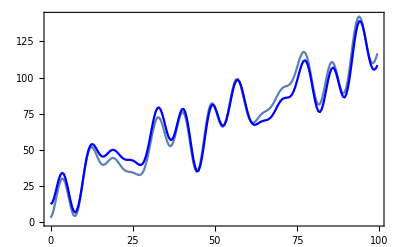

```mathematica
fm1=ModelCurve[pp,nf];p1ca=ListPlot[fm1,Joined->True,Frame->True,PlotStyle->Blue];Show[p1,p1ca]
```

#### Data from tutorial

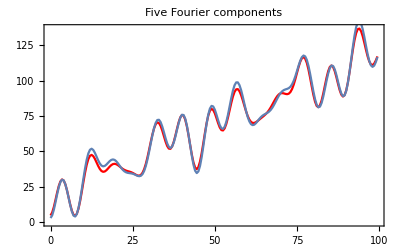

```mathematica
fm1=ModelCurve[parm5,5];p1tu=ListPlot[fm1,Joined->True,Frame->True,PlotStyle->Red,PlotLabel->"Five Fourier components"];Show[p1tu,p1]
```

#### Comparison

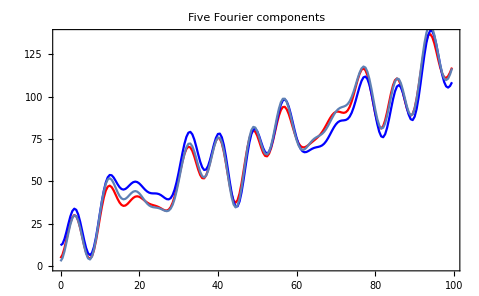

```mathematica
Show[p1tu,p1ca,p1]
```

```mathematica
,PlotStyle->{}
```

## Generalized least squares fitting (chapter 5.4)

### Generate the exact ellipse

First we create an ellipse with many points to get a nice graph.

```mathematica
m=RotationMatrix[π/3]
```

{{1/2,-(√3)/2},{(√3)/2,1/2}}

```mathematica
pts0={};n=200;Do[t=(i-1)*2 π/n;
pts0=Append[pts0,m .{0.75 Cos[t], 0.5Sin[t]}+{1,1}]
,{i,1,n}]
```

```mathematica
pts0
```

{}

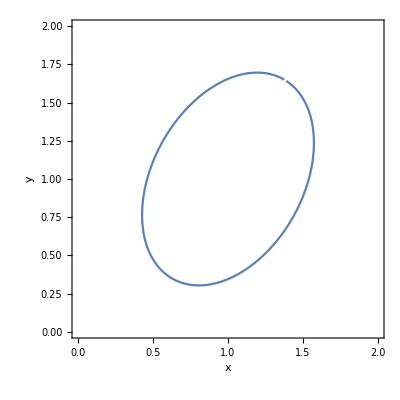

```mathematica
pp0=ListPlot[pts0,AspectRatio->1,PlotRange->{{0,2},{0,2}},Frame->True,Joined->True,FrameLabel->{"x","y"}]
```

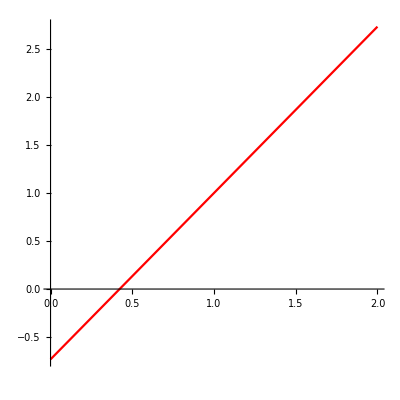

```mathematica
pg=Plot[Tan[π/3]*(x-1)+1,{x,0,2},AspectRatio->1,PlotStyle->Red]
```

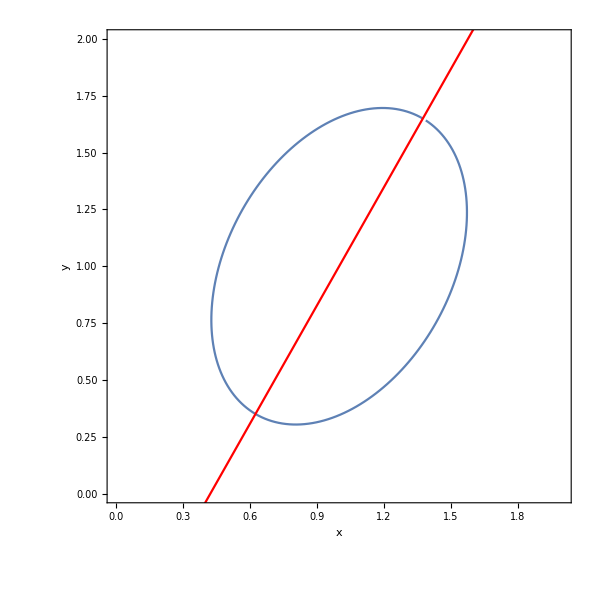

```mathematica
Show[pp0,pg]
```

Fewer points are used for the data set.

```mathematica
pts={};n=25;Do[t=(i-1)*2 π/n;
pts=Append[pts,m .{0.75 Cos[t], 0.5Sin[t]}+{1,1}]
,{i,1,n}]
```

```mathematica
pts
```

{{1.375,1.64952},{1.25553,1.69129},{1.12001,1.68962},{0.976946,1.64462},{0.83533,1.55911},{0.704062,1.43848},{0.591388,1.29029},{0.504389,1.12386},{0.448531,0.949655},{0.427324,0.778609},{0.4421,0.621474},{0.491931,0.488124},{0.573686,0.386936},{0.682228,0.324269},{0.810736,0.304061},{0.951137,0.327582},{1.09461,0.393353},{1.23213,0.497241},{1.35507,0.63272},{1.4557,0.791277},{1.5277,0.962948},{1.56654,1.13695},{1.56978,1.30234},{1.53722,1.44874},{1.4709,1.56694}}

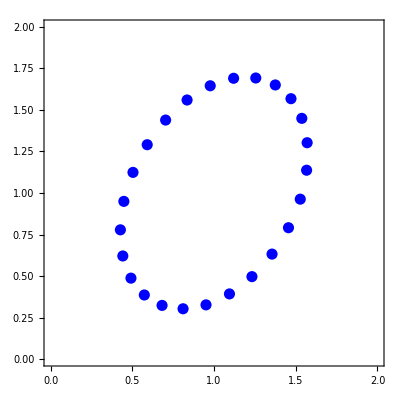

```mathematica
pp2=ListPlot[pts,AspectRatio->1,PlotRange->{{0,2},{0,2}},Frame->True, PlotStyle->{Blue,PointSize[.02]}]
```

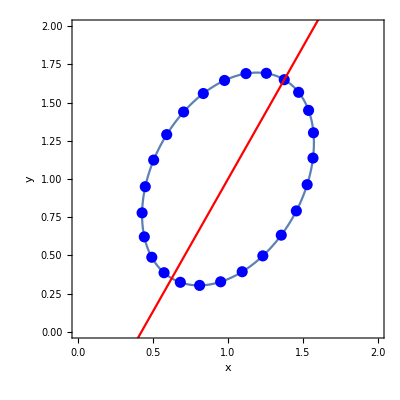

```mathematica
Show[pp0,pp2,pg]
```

### Add the noise

Create the equally distributed random numbers in a certain range.  rn0 is used in the calculations.

```mathematica
rnr=Partition[RandomReal[{-.1,.1},2n],2];
```

```mathematica
rn0={{-0.0036569789923029394,0.03594399177419505},{-0.07296691900022834,0.02841789352041535},{-0.09568396266730778,0.060106318423571226},{0.09596100193747659,0.0535682275501248},{-0.05539361652926056,0.0567472347714052},{-0.0018318142642361757,-0.09268428339745646},{0.09916232904226985,-0.08904017038714213},{-0.06526604176753706,0.04761675053677056},{-0.09715903300853468,-0.07017265413024501},{0.07177170621147988,-0.044171139694836103},{0.010341238768491134,-0.09579340860152583},{-0.01758322017799513,0.008410889299611368},{-0.018512332584362856,0.0496821590761074},{-0.014995276152327874,-0.0527430296083429},{-0.05472607853241901,-0.05698251645321889},{0.038015392952103655,-0.061400040556593205},{0.024516203037185824,0.0831668647558868},{0.06190477314499643,-0.08141412104211851},{-0.0302052550751164,0.05484980904828052},{0.04500544592087602,0.03896816628819616},{0.016811599814643363,0.0430008614303401},{-0.03638048075167083,-0.05473178756194419},{-0.05698647845553903,-0.07971707861346986},{0.043641318005886276,0.0805348621123938},{-0.05508582437435294,0.022318679404111474}};
```

Add the noise to the exact data.

```mathematica
pts1=pts+rn0
```

{{1.37134,1.68546},{1.18257,1.7197},{1.02433,1.74972},{1.07291,1.69818},{0.779937,1.61586},{0.70223,1.34579},{0.690551,1.20125},{0.439123,1.17148},{0.351372,0.879482},{0.499096,0.734438},{0.452441,0.525681},{0.474348,0.496534},{0.555174,0.436618},{0.667233,0.271526},{0.75601,0.247079},{0.989153,0.266182},{1.11912,0.47652},{1.29404,0.415827},{1.32487,0.68757},{1.50071,0.830245},{1.54451,1.00595},{1.53016,1.08222},{1.51279,1.22263},{1.58086,1.52927},{1.41582,1.58926}}

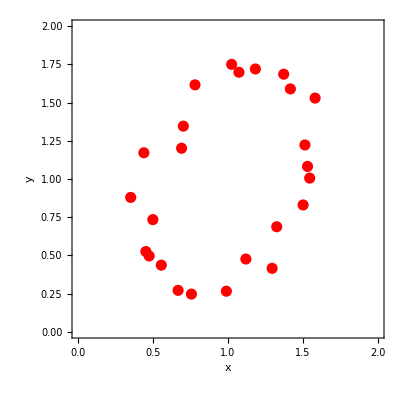

```mathematica
pp3=ListPlot[pts1,AspectRatio->1,PlotRange->{{0,2},{0,2}},Frame->True, PlotStyle->{Red,PointSize[.02]},FrameLabel->{"x","y"}]
```

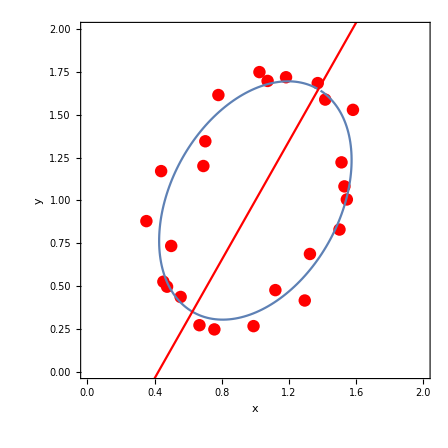

```mathematica
Show[pp3,pp0,pg]
```

```mathematica
n
```

### Export the test data

```mathematica
SetDirectory[dir<>"/../test/fit2"];
```

```mathematica
Close["test2n.dat"]
```

General::openx: test2n.dat is not open.

Close[test2n.dat]

```mathematica
Close["test2n.dat"]
```

General::openx: test2n.dat is not open.

Close[test2n.dat]

```mathematica
n=25
```

25

```mathematica
s=OpenWrite["test2n.dat",FormatType->StandardForm];
Write[s,n]
Do[Write[s,f77Eform[pts1[[i,1]],14,6],"  ",f77Eform[pts1[[i,2]],14,6]]
,{i,1,n}];Close[s]
```

test2n.dat

### Result of the fit

```mathematica
Close["test2.res"]
```

test2.res

```mathematica
parms={};Do[parms=Append[parms,Read["test2.res",{Number,Number}]],{5}]
```

```mathematica
{x0,y0,a,b,θ1}=Transpose[parms][[2]]
```

{1.00484,1.0071,0.49162,0.78586,2.67252}

```mathematica
m=RotationMatrix[θ1]
```

{{-0.891989,-0.452058},{0.452058,-0.891989}}

```mathematica
pts0={};n=200;Do[t=(i-1)*2 π/n;
pts0=Append[pts0,m .{a Cos[t], b Sin[t]}+{x0,y0}]
,{i,1,n}]
```

```mathematica
pts0
```

{}

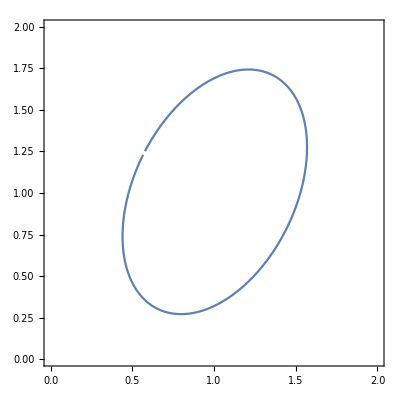

```mathematica
pp0=ListPlot[pts0,AspectRatio->1,PlotRange->{{0,2},{0,2}},Frame->True,Joined->True]
```

```mathematica
θ=θ1-π
```

-0.524709

```mathematica
θ=(θ1-π)
```

-0.469071

```mathematica
pts2={};n=200;
Do[ϕ=(i-1)*2*π/n;
rad=a ^2 b^2/(b^2Cos[ϕ-θ]^2+a^2 Sin[ϕ-θ]^2);
pts2=Append[pts2,{x0+Sqrt[rad]  Cos[ϕ],y0+Sqrt[rad] Sin[ϕ]}]
,{i,1,n}]
```

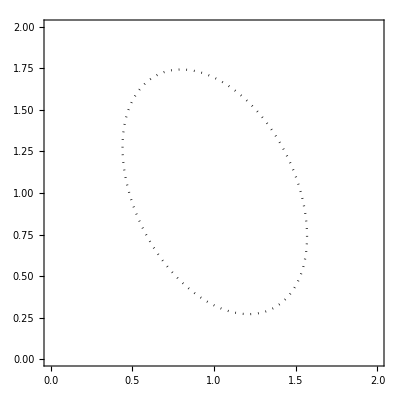

```mathematica
ppx=ListPlot[pts2,AspectRatio->1,PlotRange->{{0,2},{0,2}},Frame->True, PlotStyle->{Black,Dotted},Joined->True]
```

```mathematica
π/3.
```

1.0472

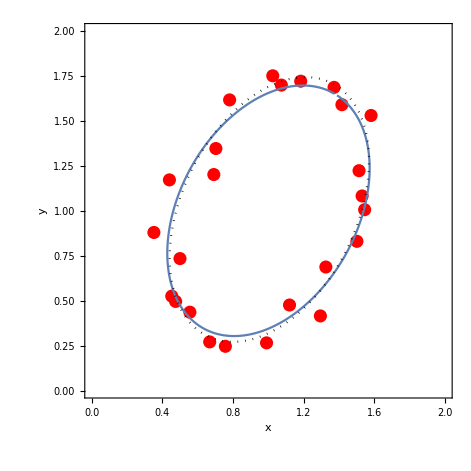

```mathematica
Show[pp3,pp0,ppx]
```

## Data modeling robust estimators

### Unit circle step by step

```mathematica
pts={};n=40;
```

```mathematica
Do[ϕ=(i-1)*π*2/n;pts=Append[pts,{1.5+Cos[ϕ],1.5+Sin[ϕ]}],{i,1,n}]
```

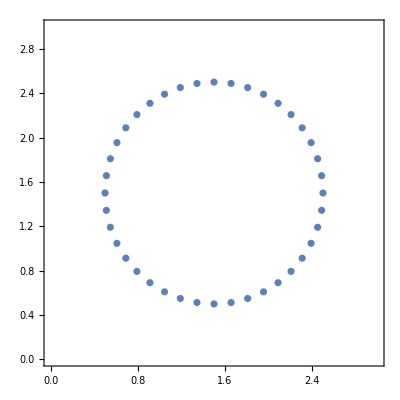

```mathematica
p1=ListPlot[pts,AspectRatio->1,Frame->True,PlotRange->{{0,3},{0,3}}]
```

```mathematica
xd=pts[[15,1]]
```

0.912215

```mathematica
pts1=pts;Do[pts1[[i]]={xd-(pts[[i,1]] -xd)/2,pts[[i,2]]} ,{i,15,27}]
```

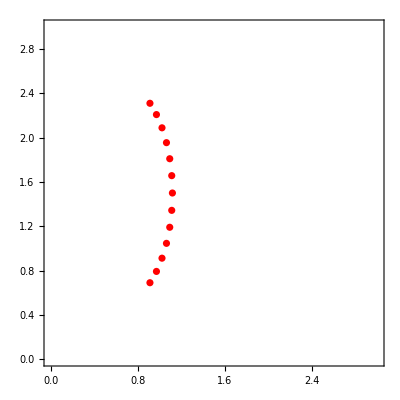

```mathematica
p2=ListPlot[pts1[[15;;27]],AspectRatio->1,Frame->True,PlotRange->{{0,3},{0,3}},PlotStyle->Red]
```

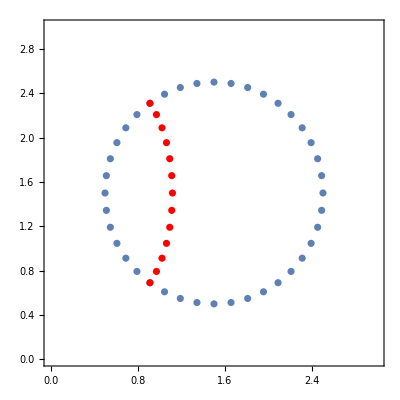

```mathematica
Show[p1,p2]
```

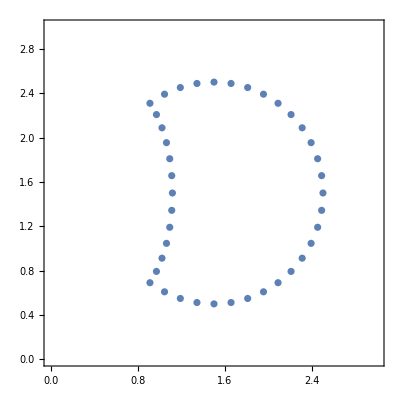

```mathematica
p2=ListPlot[pts1,AspectRatio->1,Frame->True,PlotRange->{{0,3},{0,3}}]
```

```mathematica
rand={RandomVariate[NormalDistribution[0.0,.1],40],RandomVariate[NormalDistribution[0.0,.1],40]}//Transpose
```

{{0.0340454,-0.0306125},{-0.169092,-0.0999991},{0.0552557,-0.186872},{0.0730247,0.00543546},{0.0384031,-0.180733},{0.0374984,-0.0927255},{0.00994265,0.0334149},{-0.0349998,0.0712522},{0.0324586,0.153555},{0.0383701,0.0260283},{0.0141633,-0.036012},{-0.0498074,-0.0271737},{-0.0922109,0.115021},{0.0636085,-0.220662},{0.04903,-0.115545},{-0.0323524,-0.0630875},{0.0325945,-0.0806549},{0.098916,0.101229},{0.030196,-0.0013031},{-0.0535082,0.0158411},{-0.051941,-0.000859145},{-0.115597,0.100261},{-0.155465,0.0071302},{-0.0626517,0.105684},{0.0460036,-0.0595067},{0.0297037,-0.0888937},{0.122376,-0.0101293},{0.00327809,-0.050121},{-0.123506,0.00811287},{0.0866574,0.0341006},{0.0180789,-0.0362857},{-0.104974,-0.108908},{0.0105866,-0.0353395},{0.0660523,-0.125864},{0.00448661,-0.0319665},{-0.0881193,-0.106697},{-0.0507596,0.0317918},{-0.10736,-0.200615},{-0.142011,0.00447108},{0.0232325,-0.0323312}}

```mathematica
ptr=pts1+rand
```

{{2.53405,1.46939},{2.3186,1.55644},{2.50631,1.62215},{2.46403,1.95943},{2.34742,1.90705},{2.24461,2.11438},{2.09773,2.34243},{1.91899,2.46226},{1.84148,2.60461},{1.6948,2.51372},{1.51416,2.46399},{1.29376,2.46051},{1.09877,2.56608},{1.10962,2.17034},{0.961245,2.19347},{0.939523,2.14402},{1.05543,2.00713},{1.16274,2.05522},{1.12405,1.80771},{1.05866,1.67228},{1.06638,1.49914},{0.996569,1.44383},{0.938386,1.19811},{1.00117,1.15169},{1.06883,0.852708},{1.00158,0.704},{1.03459,0.680854},{1.04929,0.558873},{1.06748,0.557056},{1.43022,0.546412},{1.51808,0.463714},{1.55146,0.403404},{1.8196,0.513604},{2.02004,0.48313},{2.09227,0.659017},{2.11899,0.686197},{2.25826,0.944007},{2.28365,0.845395},{2.30905,1.19545},{2.51092,1.31123}}

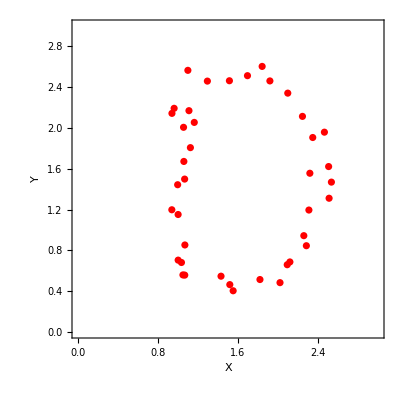

```mathematica
p2=ListPlot[ptr,AspectRatio->1,Frame->True,PlotRange->{{0,3},{0,3}},PlotStyle->Red,FrameLabel->{"X","Y"}]
```

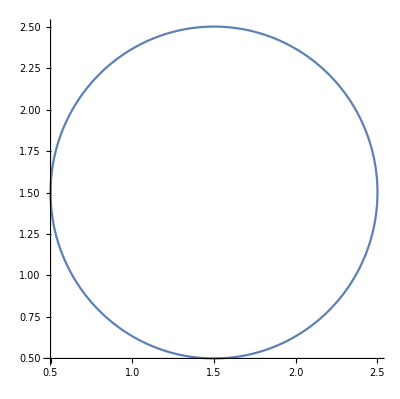

```mathematica
pp=ParametricPlot[{1.5+Cos[ϕ],1.5+Sin[ϕ]},{ϕ,0,2 π}]
```

```mathematica
cross0=Graphics[{Line[{{0,1.5},{3.0,1.5}}],Line[{{1.5,0},{1.5,3.0}}]}];
```

```mathematica
xm=1.544;ym=1.516;
```

```mathematica
cross1=Graphics[{Red,Thick,Line[{{0,ym},{3.0,ym}}],Line[{{xm,0},{xm,3.0}}]}];
```

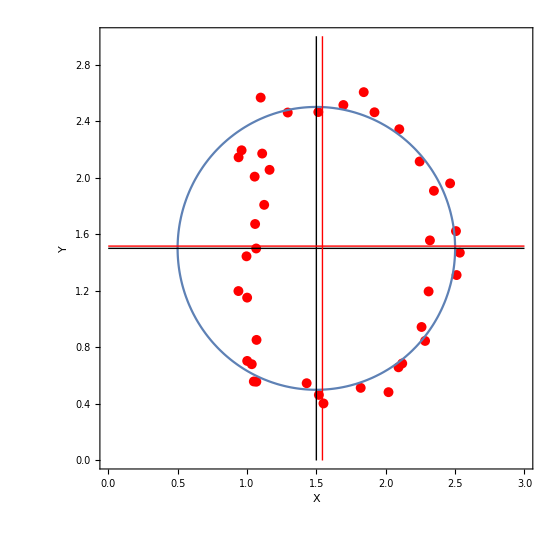

```mathematica
Show[p2,pp,cross0,cross1]
```

```mathematica
s=OpenWrite["test3.dat",FormatType->StandardForm];
Write[s,n]
Do[Write[s,f77Eform[ptr[[i,1]],14,6],"  ",f77Eform[ptr[[i,2]],14,6]]
,{i,1,n}];Close[s]
```

test3.dat